# MSc Data Science - Introduction to Programming (PX 5007) syntax and evaluation

# Marco Thiel office: Meston Building 332 Email: m.thiel@abdn.ac.uk Tel: 01224 27 3160 Twitter: @DataScienceUoA Office hours: Wednesday 1pm-2:30pm on Zoom Feedback link: https://wolfr.am/11JHosTl0 30 September, 2025

## Programming

High-level languages handle bookkeeping and repetitive tasks with ease.

Procedural Programming

Functional Programming

Pattern Matching and Rules

Parallelization and GPU Programming

## Procedural Programming

Procedural programming explicitly specifies the steps a program should take to reach the desired state or output.

### Predicate Functions

A basic tool of procedural programming is the predicate function. A predicate is a function with a range of two values, True and False. Mathematica has built-in symbols for these two values.

```mathematica
{True,False}
```

Boolean operations in Mathematica are performed similarly to the other programming languages.

x&&y, x∧y
x||y, x∨y
!x, ¬x
x⊻y
x==y
x!=y, x≠y
x>y
x<y
x≥y
x≤y | And
Or
Not
Xor
Equal
Unequal
Greater
Less
GreaterEqual
LessEqual

Here is a basic example of a predicate function used to determine the equality of two expressions.

```mathematica
2^2==4
```

Predicate functions can be strung together. Here And (&&) is used to combine Equal (==) with Greater (>).

```mathematica
3^3==27&&2>Pi
```

## Procedural Programming

### The If Statement

The if-then-else statement is a basic procedural tool defining a course of action for when a test returns true and a course of action for when a test returns false. The conditional statement if-then-else can be realized in Mathematica by If.

```mathematica
If[3>0,"Positive","Negative"]
```

It could be used as a statement.

```mathematica
x=104729;
If[PrimeQ[x],y=x,y=NextPrime[x]];y
```

It could also be used as an expression returning a value.

```mathematica
x=104731;
y=If[PrimeQ[x],x,NextPrime[x]]
```

### Exercise

Create an If statement that checks if a number is even and has two digits.

```mathematica
num=RandomInteger[{1,150}]
```

```mathematica
numtest=
```

Solution

## Loops

Loop constructs can be realized in Mathematica using Do, For, or While. These functions do not return a value unless the body of the function has created a value. Here is a Do loop that does not create or return a value.

```mathematica
Table[k,{k,13,1,-1}]
```

```mathematica
Table[Table[k,{k,1,i}],{i,1,6}]
```

```mathematica
Table[k,{i,1,6},{k,1,i}]
```

```mathematica
Do[Print[Table[k,{k,1,i}]],{i,1,6}]
```

Example: Calculate the product of a list of numbers. The TimesBy (*=) function is used here to assign the product value. Particular attention should be paid to the order of the arguments in each of these examples.

```mathematica
MatrixForm[mat=RandomReal[10,{3,3}]]
```

```mathematica
mat//Inverse
```

```mathematica
mat.%
```

```mathematica
MatrixForm[%]
```

```mathematica
EdgeDetect[CurrentImage[]]
```

```mathematica
list=RandomReal[{-1,1},100];
```

```mathematica
product1=1.;Do[product1*=list[[n]],{n,1,Length[list]}];
product1
```

```mathematica
Do[n,{n,1,Length[list]}]
```

```mathematica
For[product2=1.;n=1,n≤Length[list],n++,product2*=list[[n]]];
product2
```

```mathematica
product3=1.;n=1;
While[n≤ Length[list],product3*=list[[n]];n++];
product3
```

### Exercise

Create a Do, For, and While loop to add up all the numbers in “list.”

```mathematica
list=RandomReal[{-1,1},200];
```

```mathematica
Button["Solution",NotebookPut[Notebook[{Cell[
"sum1=0.;Do[sum1+=list[[n]],{n,1,Length[list]}];\nsum1\n
For[sum2=0.;n=1,n≤Length[list],n++,sum2+=list[[n]]];
sum2\n
sum3=0.;n=1;
While[n≤ Length[list],sum3+=list[[n]];n++];\nsum3
","Input"]}]]]
```

Solution

Use built in Mathematica functions to do the same with less code.

```mathematica
total=0.;For[i=1,i≤Length[list],i++,total=total+list[[i]]];total
```

```mathematica
Sum[list[[i]],{i,1,Length[list]}]
```

```mathematica
Fold[Plus,list]
```

```mathematica
Total[list]
```

```mathematica
Plus@@list
```

## Variable Localization

Any time you assign a value to a symbol in Mathematica, that value can influence the outcomes of other evaluations. To avoid these sorts of problems, it is advisable to localize variables whenever possible. There are two ways to localize variables in Mathematica: Module and Block.

Example: Calculate the product of a list of numbers by Do.

```mathematica
list=RandomReal[{-1,1},100];
```

```mathematica
product=0;
```

```mathematica
Module[{product=1.},
Do[product*=list[[n]],{n,1,Length[list]}];
product]
```

```mathematica
Block[{product=1.},
Do[product*=list[[n]],{n,1,Length[list]}];
product]
```

```mathematica
product
```

Module and Block work interchangeably in many situations. However, they localize the symbols in different ways.

```mathematica
x=5;
```

Module creates a temporary assignment for all specified variables during the evaluation.

```mathematica
Module[{x},Print[Expand[(1+x)^2]]]
```

Block suspends any existing assignment for all specified variables during the evaluation. When the execution of the block is finished, the original values of these symbols are restored.

```mathematica
Block[{x},Print[Expand[(1+x)^2]]]
```

## Functional Programming

Functional programming uses functions as building blocks in programming. It provides an efficient, elegant way to represent common computations. Functions can be passed as arguments into higher-order functions to perform routine and recursive tasks.

### Range and Table

Mathematica has built-in functions that could build up vectors, matrices, tensors, etc. easily. These functions provide the basic data structures that will be used in a functional programming approach.

Example: Create a matrix M where M[[n,1]]=((n-1)π)/10, M[[n,2]]=Sin[((n-1)π)/10], and 1≤ n≤ 11.

Range (generate a list of values for x).

```mathematica
x=Range[0.,Pi,0.1Pi]
```

Table (create the matrix M by iterating over the index, n).

```mathematica
Table[{x[[n]],Sin[x[[n]]]},{n,1,Length@x,1}]
```

Alternatively, the list of values can be used directly in the iterator.

```mathematica
Table[{n,Sin[n]},{n,x}]
```

An alternative approach uses the Listable attribute of Sin.

```mathematica
Transpose[{x,Sin[x]}]
```

### Exercises

Create a list of integers between 1 and 100 that are divisible by 7.

Solution

Create a list of 100 random numbers between 0 and 1.

Hint: use RandomReal

Solution

Create a 6×3 matrix with the rows containing the row number and two random numbers.

Solution

Create a multiplication table for numbers from 1 to 10.

Solution

## Built-in Recursive Functions: Fold and Nest

The Fold function can be used for recursively processing the constituent parts of a list to build up a return value.

```mathematica
f/@{a1,a2,a3,a4}
```

{f[a1],f[a2],f[a3],f[a4]}

```mathematica
x=.
```

```mathematica
Fold[f,x,{a1,a2,a3,a4}]
```

Example: Form a number from digits.

```mathematica
digits2Num[x_,y_]:=10x+y;
```

```mathematica
Fold[digits2Num,0,{1,2,3,4,5}]
```

```mathematica
FromDigits[{1,2,3,4,5}]
```

```mathematica
digits2Num[digits2Num[digits2Num[0,1],2],3]
```

When learning to use these, it is informative to use the list form to see all intermediate values.

```mathematica
FoldList[digits2Num,0,{1,2,3,4,5}]
```

The Nest function can be used to apply a function on an expression repeatedly.

```mathematica
Nest[f,x,5]
```

Again, the list form shows all of the intermediate values.

```mathematica
NestList[f,x,5]
```

```mathematica
NestList[Cos,RandomReal[],10]
```

### Exercises

Use Fold to make an alternating sum (a-b+c-d+e) from a list of letters.

```mathematica
letters={a,b,c,d,e};
```

Solution

Use NestList to calculate compound interest, outputting the amount at every month, from these values.

```mathematica
initialAmount=1000;
interestRate=0.03;
numberOfMonths=12;
```

Hint: you might want to make a function to add interest to an amount.

Solution

## Map

Map is a powerful function that maps a function to elements within an expression (including a list).

```mathematica
Map[f,{a,b,c}]
```

```mathematica
f/@{a,b,c}
```

It also lets you specify the level at which the function should be mapped. The default levelspec is 1. Map[f, expr, levelspec] will apply f from level 1 down to levelspec.

```mathematica
list={1,2,{a,b},3,4,{{c,d},{e,f}},5,6};
```

```mathematica
TreeForm[list]
```

```mathematica
Map[fun,list,3]
```

An individual level can be specified by placing levelspec in a list.

```mathematica
Map[fun,list,{3}]
```

Map can be used with expressions other than a list.

```mathematica
Map[fun,a+b+c+d+e]
```

fun[a]+fun[b]+fun[c]+fun[d]+fun[e]

Shorthand form of Map: /@. In the following example, what happens if the letters a, b, c, d, and e are replaced by numbers?

```mathematica
fun/@(a+b+c+d+e)
```

### Exercises

Using Map, create a list of powers of 2 from 1 to 1024.

Hint: you may want to define a function powerOfTwo.

Solution

Calculate the sums of the rows in the matrix mat2.

```mathematica
mat2=Table[RandomReal[],{i,5},{j,7}]
```

Solution

Calculate the mean of the length of words in Alice in Wonderland (given in aliceWords).

```mathematica
aliceWords=StringSplit[ExampleData[{"Text","AliceInWonderland"}]];
```

A summary of the list. (Alternatively, you could use TextWords.)

```mathematica
Short[aliceWords]
```

Solution

Alternatively, you could use TextWords. Check whether that gives the same result. If not, what’s the difference?

## Thread and Apply

Thread[f[args]] threads a function f over lists that appear in the provided argument.

```mathematica
Thread[f[{a,b,c},{1,2,3}]]
```

We can use that to make trainings sets for machine learning.

```mathematica
Rule@@@Transpose[{{"class","age","sex"},{"1st",32,"female"}}]
```

```mathematica
Thread[Rule[{"class","age","sex"},{"1st",32,"female"}]]
```

```mathematica
MatrixForm[{{"class","age","sex"},{"1st",32,"female"}}]
```

```mathematica
MatrixForm[Transpose[{{"class","age","sex"},{"1st",32,"female"}}]]
```

```mathematica
Thread[{a,b,c}->{1,2,3}]
```

```mathematica
Thread[{{a,b,c},{1,2,3}}]
```

Thread requires all arguments to be of equal length or single elements.

```mathematica
Thread[{{a,b,c},AA,{1,2,3}}]
```

```mathematica
Thread[{{"name1","name2","name3"},"Unknown",{34,27,38}}]
```

```mathematica
Dataset[{<|"age"->1,"money"->2,"number of cars"->3|>,
<|"age"->10,"money"->20,"number of cars"->1|>}]
```

Apply replaces the head of the expression to which it is applied. It uses the form Apply[f, expr]. You could also use @@, which is the shorthand form.

```mathematica
Apply[g,f[a,b,c]]
g@@f[a,b,c]
```

```mathematica
Apply[Plus,{1,2,3}]
```

```mathematica
Plus[1,2,3]
```

The head of an expression can be obtained by using the function Head.

```mathematica
Head[{a,b,c,d,e}]
```

Change the head from List to Times by using Apply.

```mathematica
Apply[Times,{a,b,c,d,e}]
```

## Anonymous Functions

Anonymous functions are easily created in Mathematica using Function and are very convenient when working with functions such as Map. Two things are needed in defining an anonymous function:

an ordered list giving the arguments used

a rule for combining the arguments to give the value returned by the function

Slot (#n) can be used to identify the arguments, in which case the ordered list of arguments need not be explicitly stated. Names can be assigned to anonymous functions, but naming them is not required.

Following are five equivalent ways of defining and using the anonymous function f(x)=x^2+exp(x)-3.

```mathematica
f1[x_]:=x^2+Exp[x]-3
```

```mathematica
g1[x_,y_]:=Cos[x^2+y^2]Exp[-0.1(x^2+y^2)]
```

```mathematica
Plot3D[Cos[#1^2+#2^2]Exp[-0.1(#1^2+#2^2)]&[x,y],{x,-6,6},{y,-6,6},PlotPoints->70,PlotRange->All]
```

```mathematica
f2=Function[{x},x^2+Exp[x]-3];
f2[1]
```

```mathematica
f3=Function[#^2+Exp[#]-3];
f3[1]
```

```mathematica
f4=(#^2+Exp[#]-3)&;
f4[1]
```

```mathematica
(#^2+Exp[#]-3)&[1]
```

```mathematica
f5=x ↦x^2+Exp[x]-3;
```

## Anonymous Functions

The strength of an anonymous function is the minimal effect it has. Since an anonymous function has no side effects and does not have to be assigned to a symbol, you can perform a quick transformation of data with little impact further on. A common use is with the Map function. Here is a list with various kinds of elements.

```mathematica
thisList = {a,12,"hello",{3,4/5},Plus[a,b]}
```

By using an anonymous function, you could check for what elements are integers.

```mathematica
Head[a]
```

```mathematica
Map[Head[#]===Integer&,thisList]
```

Alternatively, you could use an anonymous function to transform data.

```mathematica
data = Table[i,{i,0,2 Pi,0.1}]
```

```mathematica
ListLinePlot[Transpose[{data,Map[Sin[#]^2&,data]}]]
```

Of course, it can be helpful to use anonymous functions in a variety of situations. Using NestList, you can quickly determine the results of interest compounded annually.

Morgage £300000 over 30 years

```mathematica
ListLinePlot[NestList[1.05 # &,1000,120]]
```

Here is a set of amplitudes.

```mathematica
amplitudes = Table[Exp[-i/10.],{i,10,100,10}]
```

The amplitudes correspond to frequencies.

```mathematica
frequencies = Table[i,{i,10,100,10.}]
```

You can use Thread with an anonymous function to generate the wavefunction.

```mathematica
Thread[#1 Sin[#2 x]&[amplitudes,frequencies]]
```

### Exercises

Turn this function into an anonymous function.

```mathematica
newton[f_,x0_]:=x0-f[x0]/f'[x0]
```

Solution

## Pattern Matching and Rules

Pattern matching is used in Mathematica for checking the presence of certain pattern(s) within an expression. It could be used with Rule for modifying/replacing the existing expressions. Pattern matching and Rule could be used to perform complex tasks much more efficiently than using procedural programming. To see if a pattern is matched, MatchQ is used.

### Basic Patterns

The pattern of a single expression is represented by underscore _ (Blank).

```mathematica
MatchQ[{a,b,c},_]
```

```mathematica
ExampleData[]
```

```mathematica
dataTitanic=ExampleData[{"MachineLearning","Titanic"},"Data"];
```

```mathematica
dummy =dataTitanic[[All,1]]/.Missing[]->Nothing;
```

```mathematica
RandomSample[dummy[[1]]]
```

```mathematica
dataraw=RandomSample@dummy;
```

```mathematica
(Select[dataraw,MatchQ[#,{_,_,_}]&])[[1;;10]]
```

```mathematica
Table[{i,i^2,i^3},{i,1,10}]
```

```mathematica
Flatten[
{Select[#,#=="1st"||#=="2nd"||"3rd"&],
Select[#,NumberQ],
Select[#,#=="male"||#=="female"&]}
]&/@

(Select[dataraw,MatchQ[#,{_,_,_}]&])
```

```mathematica
(************)
```

```mathematica
completedata=(Select[dataraw,MatchQ[#,{_,_,_}]&]);
```

The

```mathematica
selectClass[x_]:=Select[x,#=="1st"||#=="2nd"||"3rd"&]
(*this selects the class*)
```

```mathematica
selectAge[x_]:=Select[x,NumberQ]
```

```mathematica
selectSex[x_]:=Select[x,#=="male"||#=="female"&]
```

```mathematica
Flatten[{selectClass[#],selectAge[#],selectSex[#]}]&/@completedata
```

```mathematica
{#[[2]],#[[1]],#[[3]]}&/@Select[(Sort/@dataraw),MatchQ[#,{_,_,_}]&]
```

```mathematica
Cases[dummy,{_,_,_}]
```

```mathematica
Length/@GatherBy[Select[dummy,MatchQ[#,{_,_}]&],First]
```

```mathematica
Select[dummy,Length[#]==3&]
```

```mathematica
Select[{{a,b,c},{x,t},{},"hellow"},MatchQ[#,{___}]&]
```

```mathematica
MatchQ[{a,b,c},{___}]
```

```mathematica
MatchQ[{},{___}]
```

```mathematica
MatchQ[{},{_,_,_}]
```

Structured patterns can be used.

```mathematica
MatchQ[3,_Integer]
```

```mathematica
MatchQ[3.,_Real]
```

```mathematica
With[{pt={3,4.2,RandomReal[1,3]}},If[MatchQ[pt,{_Integer,_Real,_List}],Graphics[{RGBColor@@pt[[3]],Point[pt[[;;2]]]},Frame-> True, ImageSize-> Small],$Failed]]
```

You can also add conditions on a pattern by using Condition (/;). Here a name is given to the Blank so Condition can be used to check to see if it is odd. The name is placed before the Blank.

```mathematica
MatchQ[7.0,x_/;OddQ[x]]
```

```mathematica
MatchQ[7.0,x_/;OddQ[x]]
```

Note that 7.0 is not an exact number, so Mathematica treats it as neither even nor odd. However, 7 is an integer and is odd.

```mathematica
OddQ[7]
```

```mathematica
MatchQ[#,x_/;OddQ[x]]&/@{7,{9,7},8}
```

There is also PatternTest (?) that can be used to check patterns, such as OddQ.

```mathematica
MatchQ[7,x_?OddQ]
```

### Exercises

What is the most specific and the most general pattern to match the string “Programming”?

Answer

Create a pattern to match any list.

Solution

Create a pattern to match a list with one element.

Solution

Create a pattern to match a list with three elements, where the first element is an odd prime and the second element is a string.

Solution

## Pattern Matching on Defining Functions

Pattern matching is used commonly in Mathematica to define functions. It allows you to restrict the argument of a function to a certain type. If the type of the argument does not match with the pattern, the expression is not evaluated.

```mathematica
fun[x_]:=x^2
```

This function is only evaluated where the argument is an integer.

```mathematica
intfun[x_Integer]:=x^2
```

```mathematica
intfun[2.]
```

Example: Fibonacci number.

```mathematica
fib[n_Integer/;n≥2]:=fib[n]=fib[n-1]+fib[n-2]
fib[0]=0;
fib[1]=1;
```

```mathematica
fib[10]
```

```mathematica
gib[n_Integer/;n≥2]:=gib[n-1]+gib[n-2]
gib[0]=0;
gib[1]=1;
```

```mathematica
AbsoluteTiming[fib/@Range[1,30]]
```

{0.000206,{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}}

```mathematica
AbsoluteTiming[gib/@Range[1,30]]
```

{6.67118,{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}}

```mathematica
?fib
```

```mathematica
fib/@Range[-3,10]
```

### BenchmarkPlot

```mathematica
ResourceFunction["BenchmarkPlot"][fib,#&,Range[10,30]]
```

```mathematica
ResourceFunction["BenchmarkPlot"][gib,#&,Range[10,30]]
```

## Pattern Matching on Defining Functions

### Using Multiple Definitions

Multiple definitions can be given to a function, and Mathematica will attempt to use the definition that matches most specifically when you use the function.

Here are four definitions for the function isFour, given in increasing order of generality. Notice that the final definition does not label the argument since the argument is not used on the right-hand side.

```mathematica
isFour[4]:="Yes!!";
isFour[x_Integer]:="No, but "<>ToString[x]<>" is an integer!";
isFour[x_?NumericQ]:="No, but "<>ToString[x]<>" is a number.";
isFour[_]:="No, not even close to four...";
```

The number 4 matches all of the patterns given in the function definitions, but the most specific match is used.

```mathematica
isFour[2]
```

View the definition for isFour.

```mathematica
?isFour
```

### Exercises

Define a function that will calculate the cube of x if x is a real number.

Solution

Define a function that, given a list with two elements, will return a list where the order of the elements is reversed.

Solution

Define a predicate (a function that returns True or False) that, given a list with two elements, checks whether the first element is larger than the second one.

Solution

#### Advanced

Define a function invert(x)=1/x that only evaluates when the input x is not 0.

Solution

## ReplaceAll

To replace expressions that match certain patterns within a list, a convenient way is to use ReplaceAll. The following commands show a possible way to handle a badly formatted dataset with the pattern-matching technique.

```mathematica
SetDirectory[NotebookDirectory[]];
(mat=Import["Data/dataset.txt","Data"])//MatrixForm
```

```mathematica
mat
```

Use a rule with ReplaceAll (/ .) to transform all of the instances of “N/A” to the integer 0.

```mathematica
mat/."N/A"->0//MatrixForm
```

To replace all the string elements with 0, use the pattern _String.

```mathematica
mat/._String->0//MatrixForm
```

RuleDelayed ( :> ) must be used if the right hand side is a function of the left hand side.

```mathematica
mat/.(a_/;a<0:> f[a])//MatrixForm
```

### Exercises

Replace the rows in mat that have “N/A” in the first position with Missing[“NotAvailable”].

Missing[“NotAvailable”] is used in Mathematica to show that data is missing. The string should contain the reason data is missing and can be anything. “NotAvailable” is a commonly used string. Many functions automatically ignore those elements.

Solution

Suppose that mat1 contains some data where all the numbers are measurements that should be non-negative. Due to measurement errors some of them are negative. Replace all negative numbers in mat1 with $Failed.

$Failed is a commonly used symbol in Mathematica to show that something has failed.

```mathematica
mat1={{"Example1",-1,97,0.39835,0.62892},
{"Example2",1,31,-0.10853,-0.92947},
{"Example3",0,91,0.46308,0.96756},
{"Example4",3,4,0.86588,0.17588},
{"Example5",-3,36,-0.52083,0.89069}};
```

Solution

#### Advanced

Replace all negative numbers x in mat with −x.

Hint: use Condition and RuleDelayed

Solution

## Cases

Cases allows you to extract elements from an expression matching a specific pattern.

```mathematica
list={1,2.3,3,2,3.4,{3.3,3},{"one","two"},2,three};
```

```mathematica
Map[Cases[list,#]&,{_Real,_?EvenQ,a_/;a^2>2}]//TableForm
```

More complicated patterns can be searched.

```mathematica
Cases[list,{_,_}]
```

### Levelspec

Providing levelspec as a single argument will apply the Cases function at all levels down to the specified level. To specify an explicit level, levelspec must be provided as a list.

```mathematica
Cases[list,q_/;q^2>5,2]
```

```mathematica
Cases[list,q_/;q^2>5,{2}]
```

### BlankSequence

BlankSequence is the FullForm of __ (double underscore). It allows you to specify nonempty subsequences that contain one or more expressions with a particular pattern.

```mathematica
Cases[{{a,1,d},{3,d,e},{t,y,4},{x,y,5,z}},{__,_Integer,__}]
```

BlankNullSequence is the FullForm of ___ (triple underscore). It allows you to specify that anything or nothing can occur in the sequence before the pattern is matched.

```mathematica
Cases[{{a,1,d},{3,d,e},{t,y,4}},{___,_Integer,___}]
```

### Exercises

Extract rows from mat1 (defined on previous slide) where the second element is positive.

```mathematica
mat1={{"Example1",-1,97,0.39835,0.62892},
{"Example2",1,31,-0.10853,-0.92947},
{"Example3",0,91,0.46308,0.96756},
{"Example4",3,4,0.86588,0.17588},
{"Example5",-3,36,-0.52083,0.89069}};
```

Solution

Extract rows from mat1 where the third element is even and less than 50.

Solution

#### Advanced

Extract rows from mat (defined on previous slide) that do not contain any strings.

Hint: use Except

Solution

Extract rows from mat that contain two or more strings.

Solution

## Comparison of Programming Styles

Recall how you multiply a list of numbers.

```mathematica
list=RandomReal[{-2,2},100000];
```

### Procedural Programming

The procedural approach required defining a product initially to 1 and telling Mathematica to multiply each element end before printing the value of the product.

```mathematica
product=1.;Do[product*=list[[n]],{n,1,Length[list]}];product
```

### Functional Programming

In a functional approach, you can use Apply to change the Head of the list to Times.

```mathematica
Apply[Times,list]
```

Not only is the functional approach easier to code, it can also make for far faster code.

```mathematica
{AbsoluteTiming[product1=1.;Do[product1*=list[[n]],{n,1,Length[list]}];product1],
AbsoluteTiming[Apply[Times,list]]}//TableForm
```

Higher-order functions are more optimized in Mathematica compared with looping constructs.

## Parallelization and GPU Programming

Mathematica provides built-in support for both CPU- and GPU-based parallelization.

### CPU-Based Parallelization

Parallelize automatically attempts to solve the expression provided, using the CPU cores available.

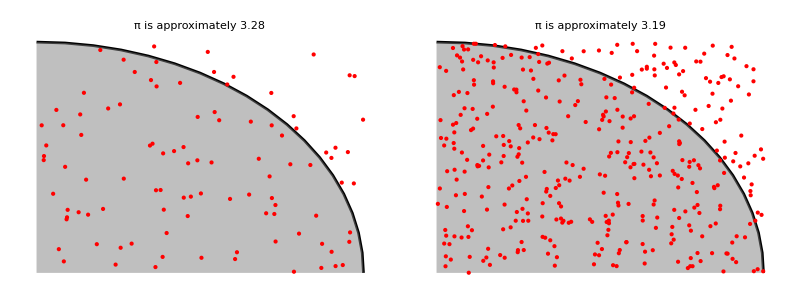

```mathematica
points=Table[RandomReal[{0,1},{i,2}],{i,100,400,300}];
Grid[Partition[Map[Graphics[{AbsoluteThickness[2],Circle[{0,0},1,{0,π/2}],GrayLevel[0.5,0.5],Disk[{0,0},1,{0,π/2}],Opacity[1],Red,AbsolutePointSize[3],Point[#]},PlotLabel->"π is approximately "<>ToString[4.0Count[ #,xy_/;Norm[xy]<1]/Length[#]]]&,points],2]]
```

```mathematica
LaunchKernels[];
f[n_Integer] := 4.0 Count[RandomReal[{0,1},{n,2}],xy_/;Norm[xy]<1]/n
DistributeDefinitions[f];
```

```mathematica
Mean[With[{n=10^6},ParallelEvaluate[f[n]]]]//AbsoluteTiming
```

```mathematica
With[{n=10^6},f[4 n]]//AbsoluteTiming
```

If the problem cannot be solved with parallel methods, the expression will be solved using normal methods.

```mathematica
Parallelize[∫(1+x^4)/(x^9+3x)ⅆx]
```

### GPU-Based Parallelization

Mathematica supports the two most widely used GPU platforms, CUDA and OpenCL, provided appropriate hardware is available. CUDA and OpenCL functions are coded and utilized in much the same way.

```mathematica
Needs["CUDALink`"]
```

```mathematica
CUDAFold[Plus,0,Range[10000000]];//AbsoluteTiming
```

```mathematica
Fold[Plus,0,Range[10000000]];//AbsoluteTiming
```

## Initialization

#### Button generation for solutions

```mathematica
Button["Solution",NotebookPut[Notebook[{Cell["SOLUTION","Input"]}]]]
```